# Homework 8 Erik Worth

## 1.

b)

c=2λ(1-2λ) so as λ varies from 1/4 to 1 c varies from 0.5(0.5) = 1/4 to 2(-1) = -2.

c)

Since z_n =a x_n+b, if z_n=0 then x_n= b/a. The parameters a and b are -4λ and 2λ respectively, so  z_n=0  corresponds to x_n= -2.

d)

```mathematica
mandelbrotC = Compile [ { cx, cy, lim },
		  Module 
		  [ { z  = 0. + I 0., ct=0},
			    While  [ Abs[z] < 2.0 && ct <= lim,
				         z = z^2 + cx + I cy; 
				         ++ct 
			         ] ;
			    -ct
		  ]
];
```

```mathematica
mandelbrotC[0.5, 0.5, 50]
```

-5

```mathematica
DensityPlot[mandelbrotC[x,y,100],{x,-2,0.6},{y,-1.3,1.3},PlotPoints->100,Mesh->False,ColorFunction->GrayLevel]
```

-Graphics-

e)

The largest cardoid is the feature traversed as c goes between 1/4 to -3/4. This is the region in the logistic map where λ varies between 1/4 and 3/4, which is the fixed point region of the logistic map. As c approaches -3/4 I would expect period doubling to occur.

f)

Following the real axis along c < -0.75 we are following λ > 3/4. This is the region where period doubling occurs, so the first blob to the left of the large cardiod is the period 2 limit cycle, and the next blob to the left is period 4, and so on.

g)

For c_□=-1.76 λ_□=0.957, where there is an island of non-chaotic behavior. Specifically at that point a period 3 limit cycle begins, and period doubling occurs as λ increases until chaotic behavior returns.

## 2.

a)

```mathematica
Lorenz = {x'[t] == -σ(x[t] - y[t]), y'[t] == - x[t]*z[t] + r*x[t] - y[t], z'[t] == x[t]*y[t] -b*z[t],x[0] == 1, y[0] == 0, z[0] == 0};
```

```mathematica
σ = 10;
```

```mathematica
r = 26.5;
```

```mathematica
b =8/3;
```

```mathematica
sol = NDSolve[Lorenz, {x,y,z}, {t, 0, 200}, MaxSteps -> 1000000];
```

```mathematica
ParametricPlot3D[{x[t], y[t], z[t]} /. sol, {t, 0, 200}, PlotPoints -> 300]
```

-Graphics3D-

NDSolve is used to solve the given set of ODEs, then ParametricPlot3D graphs the resulting stange attractor.

b)

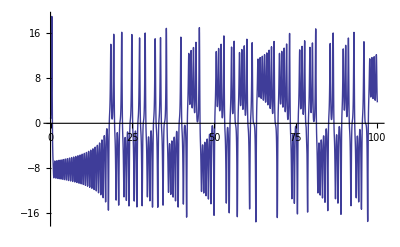

```mathematica
Plot[x[t]/.sol, {t, 0 ,100}]
```

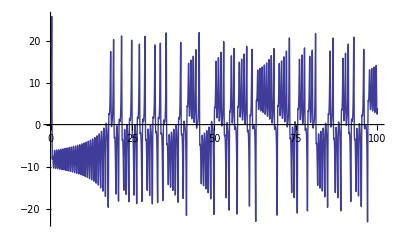

```mathematica
Plot[y[t]/.sol, {t, 0 ,100}]
```

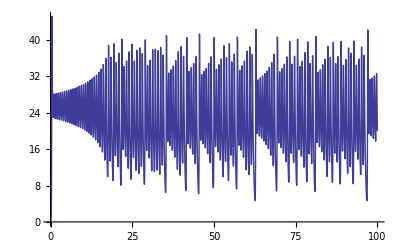

```mathematica
Plot[z[t]/.sol, {t, 0 ,100}]
```

After a short transient period all three graphs begin to oscillate in a seemingly chaotic way.

## 3.

a)

```mathematica
Clear["Global`*"]
```

```mathematica
a = 1/2;
```

```mathematica
Ω=2/3;
```

```mathematica
reduce[θ_] := Mod[θ, 2Pi] /; Mod[θ, 2Pi] ≤ Pi;
reduce[θ_] := (Mod[θ, 2 Pi] - 2Pi)/; Mod[θ, 2Pi] > Pi;
```

```mathematica
cycles = 100;
```

```mathematica
solution[ f_] := 
  NDSolve[ {w'[t]==-Sin[θ[t]]-0.5*w[t]+f Cos[Ω t], θ'[t]== w[t], θ[0] == 0, w[0] == 0}, {θ, w}, {t, 0, cycles(2Pi/Ω)}, 
    MaxSteps -> 1000000];
```

```mathematica
sol1 = solution[1];
```

```mathematica
steps = 1000;
```

```mathematica
points = Flatten[Table[{θ[t], w[t]} /. sol1, {t,0,cycles(2Pi/Ω),(1/steps)(2Pi/Ω)}], 1];
```

```mathematica
newpoints = {reduce[#[[1]]], #[[2]]}&/@points;
```

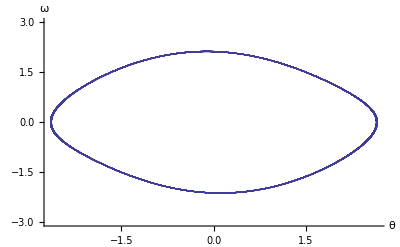

```mathematica
ListPlot[Drop[newpoints = {reduce[#[[1]]], #[[2]]}&/@(points = Flatten[Table[{θ[t], w[t]} /. sol1, {t,0,cycles(2Pi/Ω),(1/steps)(2Pi/Ω)}], 1]), 10000],PlotRange-> {-3,3}, AxesLabel -> {"θ", "ω"}, PlotStyle -> {PointSize[0.002]}]
```

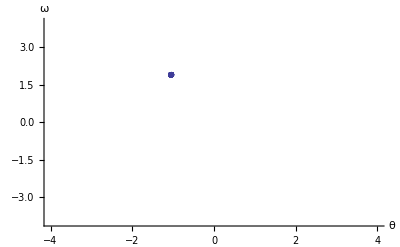

```mathematica
ListPlot[Table[newpoints[[n]], {n,1+25steps, Length[newpoints], steps}], PlotRange -> {{-4,4},{-4,4}}, AxesLabel -> {"θ", "ω"}, PlotStyle-> PointSize[0.01]]
```

Parameters a, Ω are chosen so that there are regions of chaos in the phase space plots when f is varied. The function reduce is defined to wrap the angle θ back between -π to π, and the function solution solves the differential equation for a given f. A list of points is made using Table acting on the solutions to the differential equations, then these points are fed into the reduce function to restrict θ. Listplot plots a phase space plot first, dropping the first 10,000 points. Then Table makes a list of every 1000th reduced point and Listplot makes a Poincare section from the resulting list. The phase space plot shows a period 1 limit cycle, which is made clear by the Poincare section with just one dot.

b)

```mathematica
sol2 = solution[1.5]
```

{{θ→InterpolatingFunction[{{0.,4712.39}},<>],w→InterpolatingFunction[{{0.,4712.39}},<>]}}

```mathematica
cycles = 500; steps = 100;
```

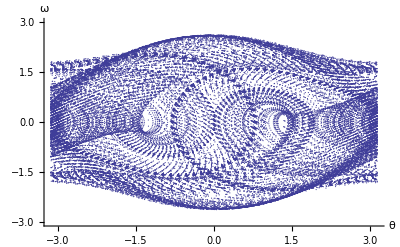

```mathematica
ListPlot[Drop[newpoints = {reduce[#[[1]]], #[[2]]}&/@(points = Flatten[Table[{θ[t], w[t]} /. sol2, {t,0,cycles(2Pi/Ω),(1/steps)(2Pi/Ω)}], 1]), 10],PlotRange-> {-3,3}, AxesLabel -> {"θ", "ω"}, PlotStyle -> {PointSize[0.002]}]
```

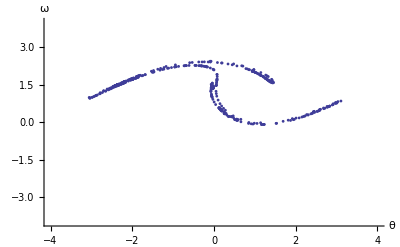

```mathematica
ListPlot[Table[newpoints[[n]], {n,1+20steps, Length[newpoints], steps}], PlotRange -> {{-4,4},{-4,4}}, AxesLabel -> {"θ", "ω"}, PlotStyle-> PointSize[0.005]]
```

Here f is taken to be 1.5 and and the same procedure as above is used. The phase space plot is very busy and appears to be chaotic; the Poincare section confirms that the f = 1.5 is a chaotic regions. No limit cycle behavior is evident.

## 4.

a)

```mathematica
dim =N[Log[4]/Log[3]]
```

1.26186

At every iteration, the curve gains 4 times as many line segments as before, but each segment is 1/3 of the length of the previous curve. So the fractal dimension is given by
log(n)/log(r) = 1.26...

b)

```mathematica
(4/3)^1
```

4/3

```mathematica
(4/3)^2
```

16/9

```mathematica
(4/3)^3
```

64/27

```mathematica
(4/3)^n
```

(4/3)^n

```mathematica
(4/3)^Infinity
```

∞

The length of the curve is (4/3)^n where n is the number of iterations, which is unbounded as n approaches infinity.

c)

```mathematica
startline =Line[{{0,0},{1,0}}]
```

Line[{{0,0},{1,0}}]

```mathematica
breakline[Line[{i_,f_}]]:=Module[{d,d3,mid},
d=f-i;
d3=d/3;
mid=Sqrt[3]/6{-d[[2]],d[[1]]}+d/2;
{
Line[{i,i+d3}],
Line[{i+d3,i+mid}],
Line[{i+mid,f-d3}],
Line[{f-d3,f}]
}]
```

```mathematica
curve[n_]:=Module[{startline},startline=Line[{{0,0},{1,0}}]//N;
Graphics[Nest[#/.x:Line[{i_,f_}]:>breakline[x]&,startline,n]]]
```

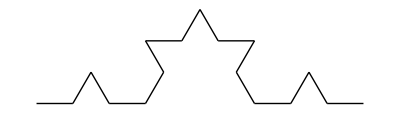

```mathematica
curve[2]
```

A line is defined with length 1. A function breakline breaks the line into 4 subsequent lines, while transforming them so that the 2 middle ones form a kink with angles equal to 60°. A function curve uses Nest to iteratively apply breakline to each line segment n times, and Graphics displays the resulting curve.

d)

```mathematica
snowflake[n_]:=Module[{startflake},startflake=Line/@{{{0,0},{1,0}},{{1,0},{1/2,-Sqrt[3]/2}},{{1/2,-Sqrt[3]/2},{0,0}}}//N;
Graphics[Nest[#/.x:Line[{_,_}]:>breakline[x]&,startflake,n],ImageSize->350]]
```

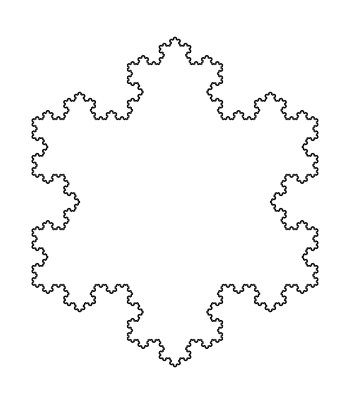

```mathematica
snowflake[5]
```

A function snowflake is defined to make Koch snowflakes. It starts with a equilateral triangle called startflake and applies the same rule as in the function curve.

## 5.

a)

```mathematica
Clear["Global`*"]
```

```mathematica
V0 = 25; L =1;
```

```mathematica
V[x_] := -.5V0(1+Cos[2Pi x/L])/; Abs[x] < L/2;
```

```mathematica
V[x_]:= 0 /; Abs[x] ≥  L/2;
```

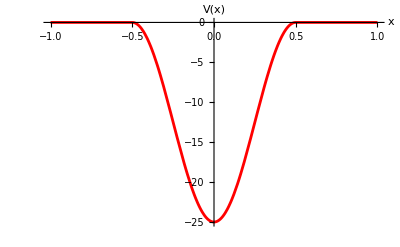

```mathematica
Plot[V[x], {x, -L, L} ,PlotStyle -> {Red, AbsoluteThickness[2]},AxesStyle -> AbsoluteThickness[0.5],  AxesLabel -> {"x", "V(x)"}]
```

The function V[x] is defined as described and the potential well is plotted from -L to L.

b)

```mathematica
B = 1;
```

```mathematica
ψ1[x_] := A Exp[ Abs[2 en]^(1/2) x]
```

```mathematica
ψ3[x_] := B Exp[- Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_] := ψ2''[x] + 2(en - V[x])ψ2[x]
```

```mathematica
wavefunc2[energy_] :=(en = energy; NDSolve[{ eqn[energy] == 0, ψ2[-L/2] ==  ψ1[-L/2], 
					ψ2'[-L/2] ==  ψ1'[-L/2]}, 
		ψ2, {x, -L/2, 0} ])
```

```mathematica
sol2[x_?NumericQ, en_?NumericQ] := ψ2[x] /. wavefunc2[en][[1]]
```

```mathematica
sol2prime[x_?NumericQ,en_?NumericQ]:=ψ2'[x]/.wavefunc2[en][[1]]
```

```mathematica
A=B;
```

```mathematica
eval = energy /.FindRoot [ sol2prime[0, energy], {energy, -25}]
```

-15.329

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2
```

```mathematica
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  <  0
```

```mathematica
ψnn[x_] := ψ1[x] /; x < -L/2
```

```mathematica
ψnn [x_] := ψ3[x] /; x > L/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

```mathematica
fig = Plot[ψ[x], {x, -1.2L, 1.2L}, PlotStyle -> {AbsoluteThickness[2], Red},AxesLabel -> {"x", "ψ"} ];
```

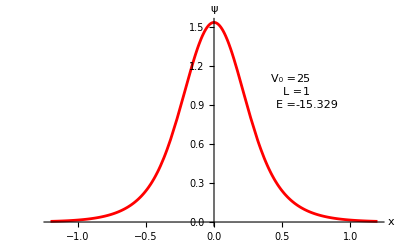

```mathematica
Show[fig,  Graphics [ { 
			Text[ en , {0.6, 0.9}, {-1, 0} ] ,
Text[ "E = ", {0.6, 0.9}, {1, 0}  ],
			Text[  V0, {0.6, 1.1}, {-1, 0} ] ,
Text[ "V_0 = ", {0.6, 1.1}, {1, 0}  ],
			Text[ "L = ", {0.65, 1}, {1, 0}], Text[ L, {0.65, 1}, {-1, 0}]  } ] ]
```

The wavefunction is defined as a decaying exponential for regions more than |L/2| away from x = 0. The wavefunction between -L/2 and L/2 is obtained by solving the differential equation with the function wavefunc2. The energy eigenvalue for the groundstate is found by using FindRoot to determine where the derivative of the wavefunction goes to zero, using the starting values of x = 0 and energy = -25. It finds the ground state eigenvalue at -15.329. The wavefunction is normalized by dividing it by normconst, which is the integral of the wavefunction squared from -∞ to ∞. The wavefunction is plotted and the plot confirms that it is the ground state because the wavefunction has no nodes.

c)

```mathematica
A= -B;
```

```mathematica
eval = en /. FindRoot [sol2[0, en] ,{en, -5} ]
```

-0.92539

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := -efunc2[-x] /; 0 ≤  x  ≤  L/2
```

```mathematica
normconst = Sqrt[NIntegrate [ ψnn[x]^2, {x, -Infinity,Infinity} ] ];
```

```mathematica
fig = Plot[ψ[x], {x, -2L,2L}, PlotStyle -> {AbsoluteThickness[2], Red},AxesLabel -> {"x", "ψ"} ];
```

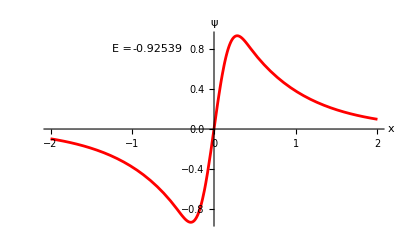

```mathematica
Show[fig,  Graphics [ { 
			Text[ en , {-1, 0.8}, {-1, 0} ] ,
Text[ "E = ", {-1, 0.8}, {1, 0}  ],
			Text[  v0, {-0.6, 1.2}, {-1, 0} ] ,
Text[ "V_0 = ", {-0.6, 1.2}, {1, 0}  ],
			Text[ "L = ", {-0.57, 1}, {1, 0}] , 	Text[ L, {-0.57, 1}, {-1, 0}]} ] ]
```

The odd parity solution is found by setting A = -B and defining the wavefunction in the region 0<x<L/2 to be the negative of the even solution there. The energy eigenvalue is found as above; FindRoot was given the initial guess of -5 and returned the eigenvalue -.925. The wavefunction is normalized as above and plotted. The resulting plot has one node and so is confirmed to be the first excited state.

## 6.

a)

```mathematica
Clear["Global`*"]
```

```mathematica
L = 6;
```

```mathematica
V[x_] := -Sech[x]^2 /; Abs[x] < 5;
```

```mathematica
V[x_] := 0 /;Abs[x] ≥  5;
```

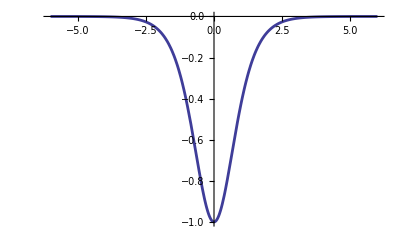

```mathematica
Plot[V[x], {x, -L, L}, PlotStyle -> {AbsoluteThickness[2]}]
```

The potential V[x] is defined as described and plotted from -L to L, where L is taken to be 6.

b)

```mathematica
B= 1;
```

```mathematica
ψ1[x_] := A Exp[ Abs[2 en]^(1/2) x]
```

```mathematica
ψ3[x_] := B Exp[- Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_] := ψ2''[x] + 2(en - V[x])ψ2[x]
```

```mathematica
wavefunc2[energy_] := (en = energy; NDSolve[{ eqn[energy] == 0, ψ2[-L/2] == ψ1[-L/2], 
					ψ2'[-L/2] == ψ1'[-L/2]}, 
		ψ2, {x, -L/2, 0} ])
```

```mathematica
sol2[x_?NumericQ, en_?NumericQ] := ψ2[x] /. wavefunc2[en][[1]]
```

```mathematica
sol2prime[x_?NumericQ,en_?NumericQ]:=ψ2'[x]/.wavefunc2[en][[1]]
```

```mathematica
A= B;
```

```mathematica
evalue=energy /. FindRoot[sol2prime[0,energy],{energy,-5, -1}]
```

-0.499976

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[evalue][[1]];
```

```mathematica
ψ [x_] := efunc2 [x] /;-L/2 ≤ x ≤ 0
```

```mathematica
ψ [x_] := efunc2 [-x] /;0 ≤ x ≤ L/2
```

```mathematica
ψ [x_] := ψ1[x] /; x < -L/2
```

```mathematica
ψ [x_] := ψ3[x]/; x > L/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψ[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψnorm[x_] := ψ[x] / normconst
```

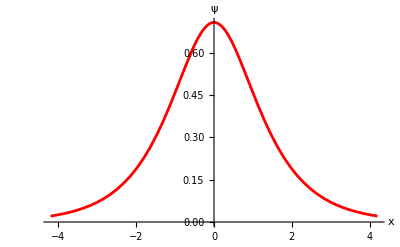

```mathematica
fig = Plot[ψnorm[x], {x, -0.7L, 0.7L}, AxesLabel -> {"x", "ψ"}, PlotStyle -> {Red, AbsoluteThickness[2]} ]
```

The same functions as in problem 5 are used again here. FindRoot returns an energy eigenvalue of -.499976, and the plot confirms that it is the ground state since there are no nodes.

c)

```mathematica
ψexact[x_]:= Sech[x]/Sqrt[2];
```

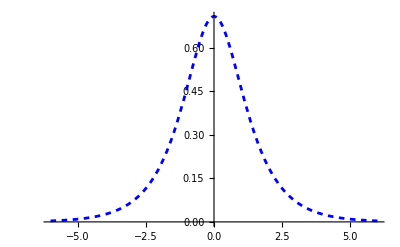

```mathematica
figexact = Plot[ψexact[x], {x, -L, L},PlotStyle -> {Blue, Dashing[{0.01, 0.01}], AbsoluteThickness[2]} ]
```

```mathematica
en = -.5;
```

```mathematica
pot[x_] := -Sech[x]^2;
```

```mathematica
ψexact''[x] + 2(en - pot[x])ψexact[x] == 0 //FullSimplify
```

True

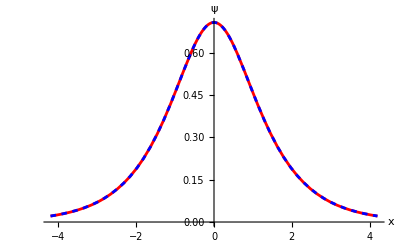

```mathematica
Show[fig, figexact]
```

The exact solution is  Sech[x]/Sqrt[2] and is plotted as a dashed blue curve. The numerical eigenvalue is very close to -.5, so I guessed that the exact solution was -0.5. When plugged into Schroedinger's equation using the exact solution, mathematica confirms that is is an eigenvalue. The exact wavefunction is then plotted on top of the numerical wavefunction; the two seem to coincide exactly at the scale of the graph.